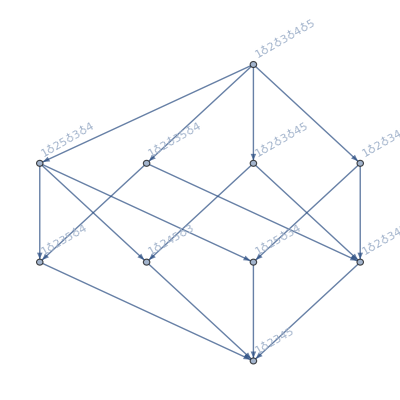
-Graphics-→-Graphics-

```mathematica
With[{k=40},
Graph[FormulaGraphReverse2[allGraphs5[k,"graph"]//FindEmptyFormula],ImageSize->400]->allGraphs5[k,"graph"]
]
```

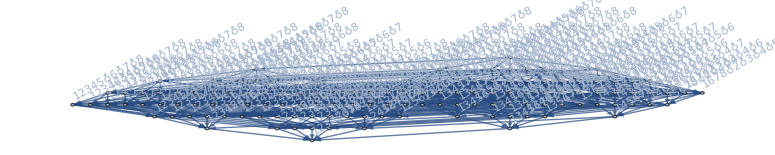
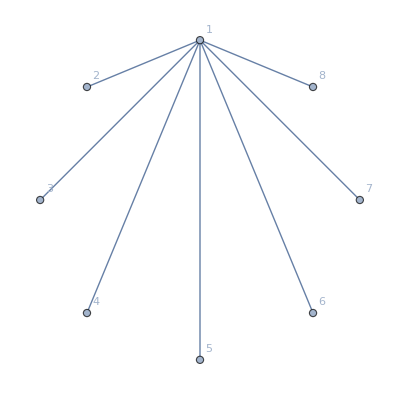
-Graphics-→-Graphics-

```mathematica
With[{g=ClawGraph[8]},
Graph[FormulaGraphReverse2[g//FindEmptyFormula],ImageSize->400]->g
]
```

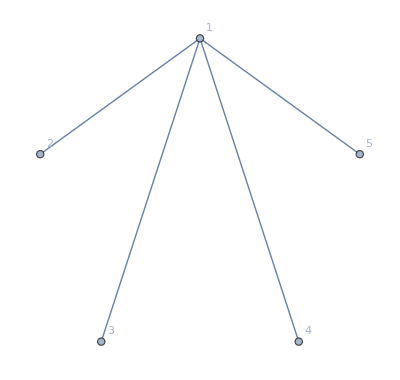

```mathematica
claw5=ClawGraph[5]
```

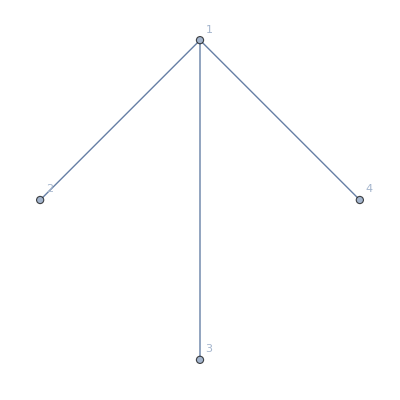

```mathematica
claw4=ClawGraph[4]
```

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[claw5,allGraphs5[#,"graph"]]&]
```

{29160,20034,6816,2278,760}

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[claw4,allGraphs5[#,"graph"]]&]//Length
```

40

```mathematica
Table[n->With[{
claw=ClawGraph[n]},Length[Select[Keys[allGraphs5],IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]]
],
{n,1,5}
]
```

{1→0,2→15,3→75,4→40,5→5}

```mathematica
allGraphs5[30586]
```

<|signature→30586,matrix→{{2,1,1,1,2},{1,2,2,2,1},{1,2,2,2,1},{1,2,2,2,1},{2,1,1,1,2}},graph→-Graphics-,vertexsets→{{1,5},{2,3,4}},vertices→{1,2},edges→{1<->2},relations→{x30586==x30406-x30496,x30586==x30406-x30496,x30586==x30082-x30334,x30586==x30082-x30334,x30586==x29938-x30262,x30586==x29938-x30262,x30586==x29097-x29826,x30586==x29128-x29857,x30586==x28218-x28308,x30586==x28218-x28308,x30586==x23518-x23770,x30586==x23518-x23770,x30586==x21186-x21510,x30586==x21186-x21510,x30586==x10228-x10552,x30586==x10228-x10552,x30586==x8184-x8436,x30586==x8184-x8436,x30586==x4132-x4222,x30586==x4132-x4222,x30586==x2124-x59048,x30586==x2124-x59048,x30586==x2124-x59048,x30586==x2124-x59048,x30586==x2124-x59048,x30586==x2124-x59048,x30586==-x1426+x697},links→{},parents→{30406,30406,30082,30082,29938,29938,29097,29128,28218,28218,23518,23518,21186,21186,10228,10228,8184,8184,4132,4132,2124,2124,2124,2124,2124,2124,697},children→{},comp→Greater,compwhy→This is a planar contraction,colofour→v15x234,colortable→{{0,v15x234},{0,v15x234},{0,v15x234},{v15x234,0},{v15x234,0},{v15x234,0},{0,v15x234},{v15x234,0},{0,v15x234},{0,v15x234}},colofournull→1/24 (-p12345+p1234x5+p1235x4+p123x45-2 p123x4x5+p1245x3+p124x35-2 p124x3x5+p125x34-2 p125x3x4+p12x345-2 p12x34x5-2 p12x35x4-2 p12x3x45+6 p12x3x4x5+p1345x2+p134x25-2 p134x2x5+p135x24-2 p135x2x4+p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5+p145x23-2 p145x2x3+p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5-11 p15x234+10 p15x23x4+10 p15x24x3+10 p15x2x34-18 p15x2x3x4+p1x2345+10 p1x234x5-2 p1x235x4-2 p1x23x45-6 p1x23x4x5-2 p1x245x3-2 p1x24x35-6 p1x24x3x5-2 p1x25x34+6 p1x25x3x4-2 p1x2x345-6 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45),colofourrealnull→-n12345+n15x234,atleast→1,atleastwhy→Comp is 'greater'.,embed→11,colofourgenerator→g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5+g1x23x4x5+g1x24x3x5+g1x2x34x5-2 g1x2x3x4x5,colotree→t15x234|>

```mathematica
Table[n->With[{
claw=ClawGraph[n]},Map[ShowGraph5Least,Select[Keys[allGraphs5],MemberQ[allGraphs5[#,"vertexsets"],{1}]&&IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]]
],
{n,1,5}
]
```

{1→{},2→{-Graphics-298881},3→{-Graphics-298262,-Graphics-297061,-Graphics-296482,-Graphics-293781,-Graphics-293281,-Graphics-292321,-Graphics-291862,-Graphics-291282,-Graphics-276101,-Graphics-268522,-Graphics-230721,-Graphics-223180,-Graphics-208121,-Graphics-200602,-Graphics-98542,-Graphics-91481,-Graphics-77380,-Graphics-70341,-Graphics-35242,-Graphics-28241,-Graphics-14262},4→{-Graphics-296464,-Graphics-293222,-Graphics-292141,-Graphics-291784,-Graphics-291662,-Graphics-291624,-Graphics-268504,-Graphics-223122,-Graphics-207942,-Graphics-200524,-Graphics-200402,-Graphics-200364,-Graphics-90944,-Graphics-75762,-Graphics-69781,-Graphics-68702,-Graphics-68184,-Graphics-30384,-Graphics-27644,-Graphics-23322,-Graphics-22841,-Graphics-12464,-Graphics-9222,-Graphics-7784},5→{-Graphics-291608,-Graphics-200348,-Graphics-68168,-Graphics-22788,-Graphics-7608}}

```mathematica
Table[n->With[{
claw=ClawGraph[n]},Length[Map[ShowGraph5Least,Select[Keys[allGraphs5],MemberQ[allGraphs5[#,"vertexsets"],{1}]&&IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]]]
],
{n,1,5}
]//Total
```

(1→0)+(2→1)+(3→21)+(4→24)+(5→5)

```mathematica
Table[n->With[{
claw=ClawGraph[n]},Map[ShowGraph5Least,Select[Keys[allGraphs5],IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]]
],
{n,1,5}
]
```

{1→{},2→{-Graphics-298881,-Graphics-305861,-Graphics-319840,-Graphics-326841,-Graphics-361940,-Graphics-368980,-Graphics-383080,-Graphics-390141,-Graphics-492201,-Graphics-499721,-Graphics-514780,-Graphics-522321,-Graphics-560121,-Graphics-567701,-Graphics-582881},3→{-Graphics-298262,-Graphics-297061,-Graphics-296482,-Graphics-293781,-Graphics-293281,-Graphics-292321,-Graphics-291862,-Graphics-304062,-Graphics-300821,-Graphics-299382,-Graphics-291282,-Graphics-319241,-Graphics-314920,-Graphics-314440,-Graphics-321982,-Graphics-312241,-Graphics-276101,-Graphics-283082,-Graphics-268522,-Graphics-361380,-Graphics-360300,-Graphics-359781,-Graphics-367361,-Graphics-354340,-Graphics-382541,-Graphics-375481,-Graphics-339160,-Graphics-346201,-Graphics-331581,-Graphics-230721,-Graphics-237701,-Graphics-223180,-Graphics-251680,-Graphics-258682,-Graphics-244141,-Graphics-208121,-Graphics-215102,-Graphics-200602,-Graphics-492122,-Graphics-492001,-Graphics-491962,-Graphics-499542,-Graphics-484602,-Graphics-514721,-Graphics-507181,-Graphics-469421,-Graphics-476942,-Graphics-461842,-Graphics-560102,-Graphics-552522,-Graphics-537342,-Graphics-424042,-Graphics-431562,-Graphics-416501,-Graphics-446621,-Graphics-401442,-Graphics-98542,-Graphics-105522,-Graphics-91481,-Graphics-119500,-Graphics-126502,-Graphics-112441,-Graphics-77380,-Graphics-84361,-Graphics-70341,-Graphics-161601,-Graphics-168641,-Graphics-154541,-Graphics-182741,-Graphics-140441,-Graphics-35242,-Graphics-42222,-Graphics-28241,-Graphics-56201,-Graphics-14262},4→{-Graphics-296464,-Graphics-293222,-Graphics-292141,-Graphics-291784,-Graphics-291662,-Graphics-291624,-Graphics-299204,-Graphics-314382,-Graphics-268504,-Graphics-359762,-Graphics-331561,-Graphics-223122,-Graphics-244082,-Graphics-207942,-Graphics-214924,-Graphics-200524,-Graphics-200402,-Graphics-200364,-Graphics-491944,-Graphics-461824,-Graphics-416444,-Graphics-401264,-Graphics-90944,-Graphics-111902,-Graphics-75762,-Graphics-82744,-Graphics-69781,-Graphics-68702,-Graphics-68184,-Graphics-154002,-Graphics-138822,-Graphics-30384,-Graphics-37364,-Graphics-27644,-Graphics-23322,-Graphics-22841,-Graphics-51341,-Graphics-12464,-Graphics-9222,-Graphics-7784},5→{-Graphics-291608,-Graphics-200348,-Graphics-68168,-Graphics-22788,-Graphics-7608}}

```mathematica
Table[n->With[{
claw=ClawGraph[n]},Select[Keys[allGraphs5],IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]
],
{n,1,5}
]//TableForm
```

1→{}
2→{29888,30586,31984,32684,36194,36898,38308,39014,49220,49972,51478,52232,56012,56770,58288}
3→{29826,29706,29648,29378,29328,29232,29186,30406,30082,29938,29128,31924,31492,31444,32198,31224,27610,28308,26852,36138,36030,35978,36736,35434,38254,37548,33916,34620,33158,23072,23770,22318,25168,25868,24414,20812,21510,20060,49212,49200,49196,49954,48460,51472,50718,46942,47694,46184,56010,55252,53734,42404,43156,41650,44662,40144,9854,10552,9148,11950,12650,11244,7738,8436,7034,16160,16864,15454,18274,14044,3524,4222,2824,5620,1426}
4→{29646,29322,29214,29178,29166,29162,29920,31438,26850,35976,33156,22312,24408,20794,21492,20052,20040,20036,49194,46182,41644,40126,9094,11190,7576,8274,6978,6870,6818,15400,13882,3038,3736,2764,2332,2284,5134,1246,922,778}
5→{29160,20034,6816,2278,760}

```mathematica
Table[n->With[{
claw=ClawGraph[n]},Select[Keys[allGraphs5],MemberQ[allGraphs5[#,"vertexsets"],{1}]&&IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]
],
{n,1,5}
]//TableForm
```

1→{}
2→{29888}
3→{29826,29706,29648,29378,29328,29232,29186,29128,27610,26852,23072,22318,20812,20060,9854,9148,7738,7034,3524,2824,1426}
4→{29646,29322,29214,29178,29166,29162,26850,22312,20794,20052,20040,20036,9094,7576,6978,6870,6818,3038,2764,2332,2284,1246,922,778}
5→{29160,20034,6816,2278,760}

```mathematica
clawKeys=Table[With[{
claw=ClawGraph[n]},Select[Keys[allGraphs5],MemberQ[allGraphs5[#,"vertexsets"],{1}]&&IsomorphicGraphQ[claw,allGraphs5[#,"graph"]]&]
],
{n,1,5}
]//Flatten
```

{29888,29826,29706,29648,29378,29328,29232,29186,29128,27610,26852,23072,22318,20812,20060,9854,9148,7738,7034,3524,2824,1426,29646,29322,29214,29178,29166,29162,26850,22312,20794,20052,20040,20036,9094,7576,6978,6870,6818,3038,2764,2332,2284,1246,922,778,29160,20034,6816,2278,760}

```mathematica
Table[ListofVars[allGraphs5[k,"colofour"]],{k,{29646,29322,29214,29178,29166,29162,29920,31438,26850,35976,33156,22312,24408,20794,21492,20052,20040,20036,49194,46182,41644,40126,9094,11190,7576,8274,6978,6870,6818,15400,13882,3038,3736,2764,2332,2284,5134,1246,922,778}}]//Flatten//DeleteDuplicates
```

{v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v145x23,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v1345x2,v134x2x5,v135x2x4,v135x24,v145x2x3,v134x25,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1245x3,v124x3x5,v125x3x4,v1235x4,v123x4x5,v1234x5,v125x34,v124x35,v123x45}

```mathematica
SetDifference[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],{v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v145x23,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v1345x2,v134x2x5,v135x2x4,v135x24,v145x2x3,v134x25,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1245x3,v124x3x5,v125x3x4,v1235x4,v123x4x5,v1234x5,v125x34,v124x35,v123x45}]
```

{v1x2x3x4x5,v12345}

```mathematica
clawfour={29646,29322,29214,29178,29166,29162,29920,31438,26850,35976,33156,22312,24408,20794,21492,20052,20040,20036,49194,46182,41644,40126,9094,11190,7576,8274,6978,6870,6818,15400,13882,3038,3736,2764,2332,2284,5134,1246,922,778}
```

{29646,29322,29214,29178,29166,29162,29920,31438,26850,35976,33156,22312,24408,20794,21492,20052,20040,20036,49194,46182,41644,40126,9094,11190,7576,8274,6978,6870,6818,15400,13882,3038,3736,2764,2332,2284,5134,1246,922,778}

```mathematica
clawfive={29160,20034,6816,2278,760}
```

{29160,20034,6816,2278,760}

```mathematica
Table[BaseCoeff[k,"C"],{k,Join[clawfive,clawfour,{29826,29706,29648,29378,29328,29232,29186,30406,30082,29938,29128,31924,31492,31444,32198,31224,27610,28308,26852,36138,36030,35978,36736,35434,38254,37548,33916,34620,33158,23072,23770,22318,25168,25868,24414,20812,21510,20060,49212,49200,49196,49954,48460,51472,50718,46942,47694,46184,56010,55252,53734,42404,43156,41650,44662,40144,9854,10552,9148,11950,12650,11244,7738,8436,7034,16160,16864,15454,18274,14044,3524,4222,2824,5620,1426}]}]//Sort//MatrixRank
```

```mathematica
vars=Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
Table[Symbol["w"<>ToString[k]]==allGraphs5[k,"colofour"],{k,Join[clawfive,clawfour]}]
```

{w29160==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w20034==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w6816==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,w2278==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,w760==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,w29646==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5,w29322==v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5,w29214==v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4,w29178==v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5,w29166==v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4,w29162==v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45,w29920==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4,w31438==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5,w26850==v145x23+v14x23x5+v15x23x4+v1x23x45+v1x23x4x5,w35976==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5,w33156==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5,w22312==v135x24+v13x24x5+v15x24x3+v1x24x35+v1x24x3x5,w24408==v1345x2+v134x2x5+v145x2x3+v14x2x35+v14x2x3x5,w20794==v134x25+v13x25x4+v14x25x3+v1x25x34+v1x25x3x4,w21492==v1345x2+v135x2x4+v145x2x3+v15x2x34+v15x2x3x4,w20052==v1345x2+v134x2x5+v15x2x34+v1x2x345+v1x2x34x5,w20040==v1345x2+v135x2x4+v14x2x35+v1x2x345+v1x2x35x4,w20036==v1345x2+v13x2x45+v145x2x3+v1x2x345+v1x2x3x45,w49194==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5,w46182==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5,w41644==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5,w40126==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5,w9094==v125x34+v12x34x5+v15x2x34+v1x25x34+v1x2x34x5,w11190==v1245x3+v124x3x5+v145x2x3+v14x25x3+v14x2x3x5,w7576==v124x35+v12x35x4+v14x2x35+v1x24x35+v1x2x35x4,w8274==v1245x3+v125x3x4+v145x2x3+v15x24x3+v15x2x3x4,w6978==v1245x3+v124x3x5+v15x24x3+v1x245x3+v1x24x3x5,w6870==v1245x3+v125x3x4+v14x25x3+v1x245x3+v1x25x3x4,w6818==v1245x3+v12x3x45+v145x2x3+v1x245x3+v1x2x3x45,w15400==v1235x4+v123x4x5+v135x2x4+v13x25x4+v13x2x4x5,w13882==v1234x5+v123x4x5+v134x2x5+v13x24x5+v13x2x4x5,w3038==v123x45+v12x3x45+v13x2x45+v1x23x45+v1x2x3x45,w3736==v1235x4+v125x3x4+v135x2x4+v15x23x4+v15x2x3x4,w2764==v1235x4+v123x4x5+v15x23x4+v1x235x4+v1x23x4x5,w2332==v1235x4+v125x3x4+v13x25x4+v1x235x4+v1x25x3x4,w2284==v1235x4+v12x35x4+v135x2x4+v1x235x4+v1x2x35x4,w5134==v1234x5+v124x3x5+v134x2x5+v14x23x5+v14x2x3x5,w1246==v1234x5+v123x4x5+v14x23x5+v1x234x5+v1x23x4x5,w922==v1234x5+v124x3x5+v13x24x5+v1x234x5+v1x24x3x5,w778==v1234x5+v12x34x5+v134x2x5+v1x234x5+v1x2x34x5}

```mathematica
vars
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
Fold[And,Table[Symbol["w"<>ToString[k]]==allGraphs5[k,"colofour"],{k,Join[clawfive,clawfour]}]]
```

w29160==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&w20034==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&w6816==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5&&w2278==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5&&w760==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5&&w29646==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5&&w29322==v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5&&w29214==v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4&&w29178==v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5&&w29166==v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4&&w29162==v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45&&w29920==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4&&w31438==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5&&w26850==v145x23+v14x23x5+v15x23x4+v1x23x45+v1x23x4x5&&w35976==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5&&w33156==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5&&w22312==v135x24+v13x24x5+v15x24x3+v1x24x35+v1x24x3x5&&w24408==v1345x2+v134x2x5+v145x2x3+v14x2x35+v14x2x3x5&&w20794==v134x25+v13x25x4+v14x25x3+v1x25x34+v1x25x3x4&&w21492==v1345x2+v135x2x4+v145x2x3+v15x2x34+v15x2x3x4&&w20052==v1345x2+v134x2x5+v15x2x34+v1x2x345+v1x2x34x5&&w20040==v1345x2+v135x2x4+v14x2x35+v1x2x345+v1x2x35x4&&w20036==v1345x2+v13x2x45+v145x2x3+v1x2x345+v1x2x3x45&&w49194==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5&&w46182==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5&&w41644==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5&&w40126==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5&&w9094==v125x34+v12x34x5+v15x2x34+v1x25x34+v1x2x34x5&&w11190==v1245x3+v124x3x5+v145x2x3+v14x25x3+v14x2x3x5&&w7576==v124x35+v12x35x4+v14x2x35+v1x24x35+v1x2x35x4&&w8274==v1245x3+v125x3x4+v145x2x3+v15x24x3+v15x2x3x4&&w6978==v1245x3+v124x3x5+v15x24x3+v1x245x3+v1x24x3x5&&w6870==v1245x3+v125x3x4+v14x25x3+v1x245x3+v1x25x3x4&&w6818==v1245x3+v12x3x45+v145x2x3+v1x245x3+v1x2x3x45&&w15400==v1235x4+v123x4x5+v135x2x4+v13x25x4+v13x2x4x5&&w13882==v1234x5+v123x4x5+v134x2x5+v13x24x5+v13x2x4x5&&w3038==v123x45+v12x3x45+v13x2x45+v1x23x45+v1x2x3x45&&w3736==v1235x4+v125x3x4+v135x2x4+v15x23x4+v15x2x3x4&&w2764==v1235x4+v123x4x5+v15x23x4+v1x235x4+v1x23x4x5&&w2332==v1235x4+v125x3x4+v13x25x4+v1x235x4+v1x25x3x4&&w2284==v1235x4+v12x35x4+v135x2x4+v1x235x4+v1x2x35x4&&w5134==v1234x5+v124x3x5+v134x2x5+v14x23x5+v14x2x3x5&&w1246==v1234x5+v123x4x5+v14x23x5+v1x234x5+v1x23x4x5&&w922==v1234x5+v124x3x5+v13x24x5+v1x234x5+v1x24x3x5&&w778==v1234x5+v12x34x5+v134x2x5+v1x234x5+v1x2x34x5

```mathematica
FindInstance[Fold[And,Table[Symbol["w"<>ToString[k]]==allGraphs5[k,"colofour"],{k,Join[clawfive,clawfour]}]],{v1234x5}]
```

FindInstance::exvar: The system contains a nonconstant expression v1235x4 independent of variables {v1234x5}.

FindInstance[w29160==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&w20034==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5&&w6816==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5&&w2278==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5&&w760==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5&&w29646==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5&&w29322==v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5&&w29214==v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4&&w29178==v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5&&w29166==v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4&&w29162==v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45&&w29920==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4&&w31438==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5&&w26850==v145x23+v14x23x5+v15x23x4+v1x23x45+v1x23x4x5&&w35976==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5&&w33156==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5&&w22312==v135x24+v13x24x5+v15x24x3+v1x24x35+v1x24x3x5&&w24408==v1345x2+v134x2x5+v145x2x3+v14x2x35+v14x2x3x5&&w20794==v134x25+v13x25x4+v14x25x3+v1x25x34+v1x25x3x4&&w21492==v1345x2+v135x2x4+v145x2x3+v15x2x34+v15x2x3x4&&w20052==v1345x2+v134x2x5+v15x2x34+v1x2x345+v1x2x34x5&&w20040==v1345x2+v135x2x4+v14x2x35+v1x2x345+v1x2x35x4&&w20036==v1345x2+v13x2x45+v145x2x3+v1x2x345+v1x2x3x45&&w49194==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5&&w46182==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5&&w41644==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5&&w40126==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5&&w9094==v125x34+v12x34x5+v15x2x34+v1x25x34+v1x2x34x5&&w11190==v1245x3+v124x3x5+v145x2x3+v14x25x3+v14x2x3x5&&w7576==v124x35+v12x35x4+v14x2x35+v1x24x35+v1x2x35x4&&w8274==v1245x3+v125x3x4+v145x2x3+v15x24x3+v15x2x3x4&&w6978==v1245x3+v124x3x5+v15x24x3+v1x245x3+v1x24x3x5&&w6870==v1245x3+v125x3x4+v14x25x3+v1x245x3+v1x25x3x4&&w6818==v1245x3+v12x3x45+v145x2x3+v1x245x3+v1x2x3x45&&w15400==v1235x4+v123x4x5+v135x2x4+v13x25x4+v13x2x4x5&&w13882==v1234x5+v123x4x5+v134x2x5+v13x24x5+v13x2x4x5&&w3038==v123x45+v12x3x45+v13x2x45+v1x23x45+v1x2x3x45&&w3736==v1235x4+v125x3x4+v135x2x4+v15x23x4+v15x2x3x4&&w2764==v1235x4+v123x4x5+v15x23x4+v1x235x4+v1x23x4x5&&w2332==v1235x4+v125x3x4+v13x25x4+v1x235x4+v1x25x3x4&&w2284==v1235x4+v12x35x4+v135x2x4+v1x235x4+v1x2x35x4&&w5134==v1234x5+v124x3x5+v134x2x5+v14x23x5+v14x2x3x5&&w1246==v1234x5+v123x4x5+v14x23x5+v1x234x5+v1x23x4x5&&w922==v1234x5+v124x3x5+v13x24x5+v1x234x5+v1x24x3x5&&w778==v1234x5+v12x34x5+v134x2x5+v1x234x5+v1x2x34x5,{v1234x5}]

```mathematica
Solve[Fold[And,Table[Symbol["w"<>ToString[k]]==allGraphs5[k,"colofour"],{k,Join[clawfive,clawfour]}]],vars]
```

{}

```mathematica
repClaw=Table[Symbol["w"<>ToString[k]]->ShowGraph5Least[k],{k,Join[clawfive,clawfour]}]
```

{w29160→-Graphics-291608,w20034→-Graphics-200348,w6816→-Graphics-68168,w2278→-Graphics-22788,w760→-Graphics-7608,w29646→-Graphics-296464,w29322→-Graphics-293222,w29214→-Graphics-292141,w29178→-Graphics-291784,w29166→-Graphics-291662,w29162→-Graphics-291624,w29920→-Graphics-299204,w31438→-Graphics-314382,w26850→-Graphics-268504,w35976→-Graphics-359762,w33156→-Graphics-331561,w22312→-Graphics-223122,w24408→-Graphics-244082,w20794→-Graphics-207942,w21492→-Graphics-214924,w20052→-Graphics-200524,w20040→-Graphics-200402,w20036→-Graphics-200364,w49194→-Graphics-491944,w46182→-Graphics-461824,w41644→-Graphics-416444,w40126→-Graphics-401264,w9094→-Graphics-90944,w11190→-Graphics-111902,w7576→-Graphics-75762,w8274→-Graphics-82744,w6978→-Graphics-69781,w6870→-Graphics-68702,w6818→-Graphics-68184,w15400→-Graphics-154002,w13882→-Graphics-138822,w3038→-Graphics-30384,w3736→-Graphics-37364,w2764→-Graphics-27644,w2332→-Graphics-23322,w2284→-Graphics-22841,w5134→-Graphics-51341,w1246→-Graphics-12464,w922→-Graphics-9222,w778→-Graphics-7784}

```mathematica
w2284==-w2764-w29162+w29166-w29322+w29646+w3736+w41644-w46182+w6818+w6978-w8274/.repClaw
```

-Graphics-22841==-Graphics-296464--Graphics-293222--Graphics-291624+-Graphics-291662--Graphics-461824+-Graphics-416444--Graphics-27644+-Graphics-69781--Graphics-82744+-Graphics-68184+-Graphics-37364

```mathematica
Table[Symbol["w"<>ToString[k]]==allGraphs5[k,"colofour"],{k,Append[clawKeys,0]}]
```

{w29888==v1x2345,w29826==v1x2345+v1x234x5,w29706==v1x2345+v1x235x4,w29648==v1x2345+v1x23x45,w29378==v1x2345+v1x245x3,w29328==v1x2345+v1x24x35,w29232==v1x2345+v1x25x34,w29186==v1x2345+v1x2x345,w29128==v15x234+v1x234x5,w27610==v14x235+v1x235x4,w26852==v145x23+v1x23x45,w23072==v13x245+v1x245x3,w22318==v135x24+v1x24x35,w20812==v134x25+v1x25x34,w20060==v1345x2+v1x2x345,w9854==v12x345+v1x2x345,w9148==v125x34+v1x25x34,w7738==v124x35+v1x24x35,w7034==v1245x3+v1x245x3,w3524==v123x45+v1x23x45,w2824==v1235x4+v1x235x4,w1426==v1234x5+v1x234x5,w29646==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5,w29322==v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5,w29214==v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4,w29178==v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5,w29166==v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4,w29162==v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45,w26850==v145x23+v14x23x5+v15x23x4+v1x23x45+v1x23x4x5,w22312==v135x24+v13x24x5+v15x24x3+v1x24x35+v1x24x3x5,w20794==v134x25+v13x25x4+v14x25x3+v1x25x34+v1x25x3x4,w20052==v1345x2+v134x2x5+v15x2x34+v1x2x345+v1x2x34x5,w20040==v1345x2+v135x2x4+v14x2x35+v1x2x345+v1x2x35x4,w20036==v1345x2+v13x2x45+v145x2x3+v1x2x345+v1x2x3x45,w9094==v125x34+v12x34x5+v15x2x34+v1x25x34+v1x2x34x5,w7576==v124x35+v12x35x4+v14x2x35+v1x24x35+v1x2x35x4,w6978==v1245x3+v124x3x5+v15x24x3+v1x245x3+v1x24x3x5,w6870==v1245x3+v125x3x4+v14x25x3+v1x245x3+v1x25x3x4,w6818==v1245x3+v12x3x45+v145x2x3+v1x245x3+v1x2x3x45,w3038==v123x45+v12x3x45+v13x2x45+v1x23x45+v1x2x3x45,w2764==v1235x4+v123x4x5+v15x23x4+v1x235x4+v1x23x4x5,w2332==v1235x4+v125x3x4+v13x25x4+v1x235x4+v1x25x3x4,w2284==v1235x4+v12x35x4+v135x2x4+v1x235x4+v1x2x35x4,w1246==v1234x5+v123x4x5+v14x23x5+v1x234x5+v1x23x4x5,w922==v1234x5+v124x3x5+v13x24x5+v1x234x5+v1x24x3x5,w778==v1234x5+v12x34x5+v134x2x5+v1x234x5+v1x2x34x5,w29160==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w20034==v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w6816==v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,w2278==v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,w760==v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,w0==v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5}

```mathematica
Solve[Fold[And,Table[Symbol["w"<>ToString[k]]==allGraphs5[k,"colofour"],{k,Append[clawKeys,0]}]],vars]
```

{}

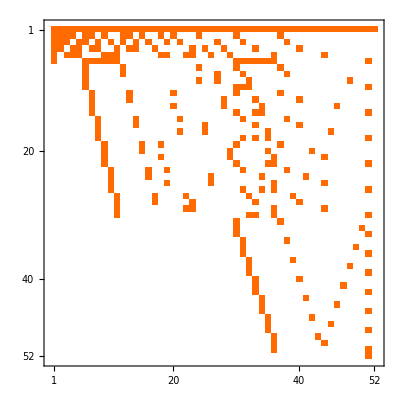

```mathematica
Table[BaseCoeff[k,"C"],{k,Append[clawKeys,0]}]//ReverseSort//MatrixPlot
```